```mathematica
SetDirectory[NotebookDirectory[]];
```

### Compare no corr and corr w=100

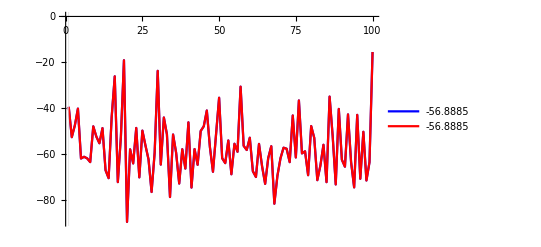

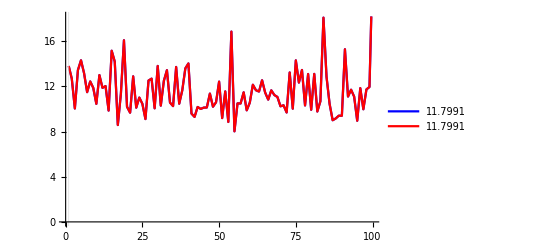

```mathematica
mmin=1;
corrdata=Import["o16test.vmc.100.dat"];
nocorrdata=Import["o16test.vmc.100.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

corrl=Length[corrE];
nocorrl=Length[nocorrE];
ipmean=Mean[corrE[[mmin;;corrl]]];
nomean=Mean[nocorrE[[mmin;;nocorrl]]];
iperr=Sqrt[Total[corrσ[[mmin;;corrl]]^2]/Length[corrσ[[mmin;;corrl]]]];
noerr=Sqrt[Total[nocorrσ[[mmin;;nocorrl]]^2]/Length[nocorrσ[[mmin;;nocorrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
```

### Stampede w=10000 (1000 ip)

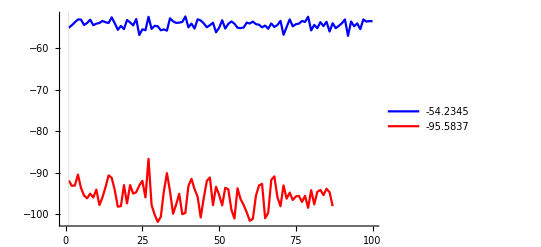

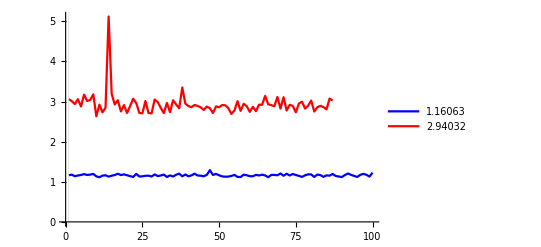

```mathematica
mmin=1;
corrdata=Import["dat.6643706"];
nocorrdata=Import["dat.6604269"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

corrl=Length[corrE];
nocorrl=Length[nocorrE];
ipmean=Mean[corrE[[mmin;;corrl]]];
nomean=Mean[nocorrE[[mmin;;nocorrl]]];
iperr=Sqrt[Total[corrσ[[mmin;;corrl]]^2]/Length[corrσ[[mmin;;corrl]]]];
noerr=Sqrt[Total[nocorrσ[[mmin;;nocorrl]]^2]/Length[nocorrσ[[mmin;;nocorrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
```

### compare Stampede w=10000 before and after update

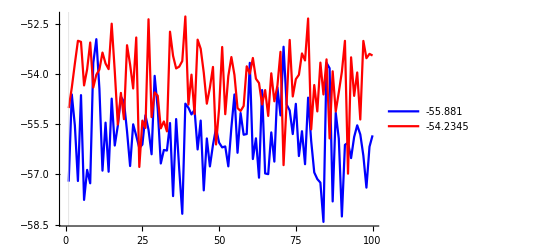

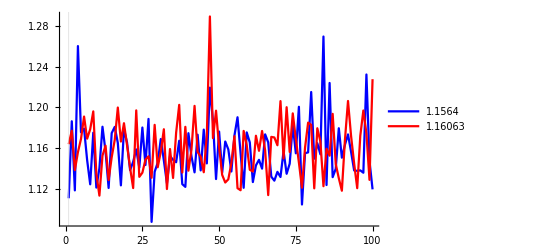

```mathematica
mmin=1;
bdata=Import["dat.6604269"];
adata=Import["dat.6643121"];
corrE=Transpose[bdata][[4]];
nocorrE=Transpose[adata][[4]];
corrσ=Transpose[bdata][[6]];
nocorrσ=Transpose[adata][[6]];

corrl=Length[corrE];
nocorrl=Length[nocorrE];
ipmean=Mean[corrE[[mmin;;corrl]]];
nomean=Mean[nocorrE[[mmin;;nocorrl]]];
iperr=Sqrt[Total[corrσ[[mmin;;corrl]]^2]/Length[corrσ[[mmin;;corrl]]]];
noerr=Sqrt[Total[nocorrσ[[mmin;;nocorrl]]^2]/Length[nocorrσ[[mmin;;nocorrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
```

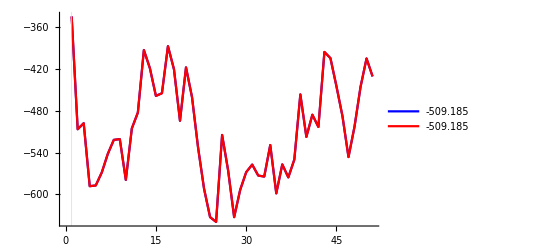

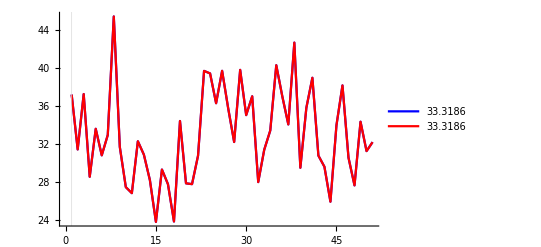

```mathematica
mmin=1;
bdata=Import["test.dat"];
adata=Import["test.dat"];
corrE=Transpose[bdata][[4]];
nocorrE=Transpose[adata][[4]];
corrσ=Transpose[bdata][[6]];
nocorrσ=Transpose[adata][[6]];

corrl=Length[corrE];
nocorrl=Length[nocorrE];
ipmean=Mean[corrE[[mmin;;corrl]]];
nomean=Mean[nocorrE[[mmin;;nocorrl]]];
iperr=Sqrt[Total[corrσ[[mmin;;corrl]]^2]/Length[corrσ[[mmin;;corrl]]]];
noerr=Sqrt[Total[nocorrσ[[mmin;;nocorrl]]^2]/Length[nocorrσ[[mmin;;nocorrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
```

### dmc Compare no corr and corr w=1000

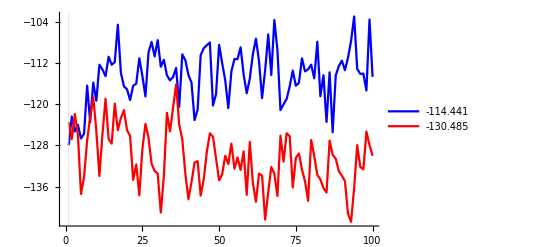

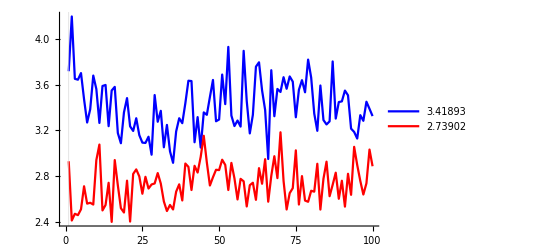

```mathematica
mmin=1;
corrdata=Import["dat.6742264"];
nocorrdata=Import["o16noip.dmc.1000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

corrl=Length[corrE];
nocorrl=Length[nocorrE];
ipmean=Mean[corrE[[mmin;;corrl]]];
nomean=Mean[nocorrE[[mmin;;nocorrl]]];
iperr=Sqrt[Total[corrσ[[mmin;;corrl]]^2]/Length[corrσ[[mmin;;corrl]]]];
noerr=Sqrt[Total[nocorrσ[[mmin;;nocorrl]]^2]/Length[nocorrσ[[mmin;;nocorrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
```

### Get Error

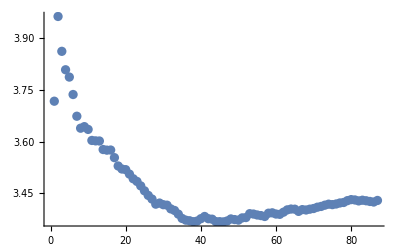

```mathematica
corrdata=Import["dat.6742264"];
nocorrdata=Import["o16noip.dmc.1000.dat"];
data = Import["o16noip.dmc.1000.dat"];
max = 87;
error = Transpose[data][[6]][[1 ;; max]];

cumerr[indata_, n_] := Module[{temp, aveerr},
  temp = indata[[1 ;; n]];
  aveerr = Sqrt[Total[temp^2]/n];
  aveerr
  ]

plotdata = Range[1, max]*0;
For[i = 1, i <= Length[error], i++,
 plotdata[[i]] = {i, cumerr[error, i]};
 ]

ListPlot[plotdata]
```